```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Radon Transform

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Aug 2018. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Imagine shining a light bright enough to pierce an object; the amount of light that reaches the other side is proportional to the amount of matter in the path. The Radon transform projects through an image (like shining a light or taking an x-ray photograph) at all possible angles. For angles where all the pixel values are small, the sum is small; for angles where there are many large pixel values, the sum is large. Each projection is displayed as one column of an image: the horizontal axis is the angle of projection and the vertical axis is proportional to the sum of the data at that angle. The Radon transform can be used to locate lines in an image (because lines block the projection in only one specific angle) and hence can be used to locate the orientation or rotation of an image such as thread x-rays.

```mathematica
TableForm[{{Hyperlink["RadonLine",{"visualVocabRadon.nb","labelRadonLine"}],labelRadonLine},{Hyperlink["RadonGrid",{"visualVocabRadon.nb","labelRadonGrid"}],labelRadonGrid},{Hyperlink["RadonRandomLines",{"visualVocabRadon.nb","labelRadonRandomLines"}],labelRadonRandomLines},{Hyperlink["RadonCircles",{"visualVocabRadon.nb","labelRadonCircles"}],labelRadonCircles},{Hyperlink["RadonTwoCircles",{"visualVocabRadon.nb","labelRadonTwoCircles"}],labelRadonTwoCircles},{Hyperlink["InvRadon",{"visualVocabRadon.nb","labelInvRadon"}],labelInvRadon},{Hyperlink["RectangleModel",{"visualVocabRadon.nb","labelRectangleModel"}],labelRectangleModel},{Hyperlink["LineFinding",{"visualVocabRadon.nb","labelLineFinding"}],labelLineFinding}}]
```

RadonLinevisualVocabRadon.nblabelRadonLinevisualVocabRadon.nb | The Radon transform (right) shows the location and orientation of the line (left)
RadonGridvisualVocabRadon.nblabelRadonGridvisualVocabRadon.nb | The Radon transform (right) shows the locations and orientations of the lines (left)
RadonRandomLinesvisualVocabRadon.nblabelRadonRandomLinesvisualVocabRadon.nb | Find the correspondences between the lines on the left and the dots in the transform on the right
RadonCirclesvisualVocabRadon.nblabelRadonCirclesvisualVocabRadon.nb | The Radon transform of a circle is an arched curve
RadonTwoCirclesvisualVocabRadon.nblabelRadonTwoCirclesvisualVocabRadon.nb | Find the correspondences between the circles on the left and the transform on the right
InvRadonvisualVocabRadon.nblabelInvRadonvisualVocabRadon.nb | The image on the left is Radon transformed (middle) and then inverted (right)
RectangleModelvisualVocabRadon.nblabelRectangleModelvisualVocabRadon.nb | Using the Radon transform to locate the vertical and hortizontal strips
LineFindingvisualVocabRadon.nblabelLineFindingvisualVocabRadon.nb | Using the Radon transform to locate major linear elements in an image

Important functions for this notebook are Radon[ ] and InverseRadon[ ] which calculate the transform and its inverse, along with ImageLines[ ] which uses the Radon transform to locate the most significant lines in an image.

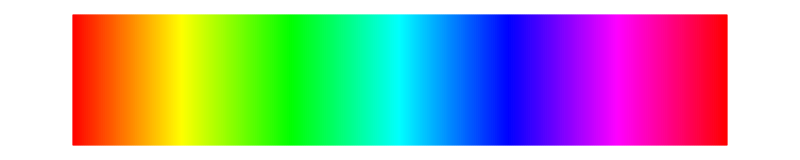

```mathematica
specLine
```

The Radon transform of a single line is shown in the following picture. The left hand image shows the line, while the right hand image shows the Radon transform, which is a bright dot in the plane. As the line moves left and right, the bright dot moves up and down. As the line tilts away from vertical, the bright dot moves left and right. The position of the dot (the maximum value in the Radon image) gives both the location and orientation of the line.

```mathematica
labelRadonLine="The Radon transform (right) shows the location and orientation of the line (left)";
infoRadonLine="A line in an image (on the left) corresponds to a bright spot in the Radon transform (on the right). Play with the position and angle of the line: here is what you will find:\n\nThe angle of the line corresponds to the horizontal position of the white dot in the tranformed space.\n\nThe left/right position of the line corresponds to the vertical height of the white dot in the transformed space.";Manipulate[img=Image[Graphics[{White,Thickness->0.02,Line[{{ρ Cos[θ]+30 Sin[θ],ρ Sin[θ]-30 Cos[θ]},{ρ Cos[θ]-30 Sin[θ],ρ Sin[θ]+30 Cos[θ]}}]},AxesOrigin->{0,0},PlotRange->{{-30,30},{-30,30}},Background->Black]];
GraphicsGrid[{{img,ImageAdjust[Radon[img,Method->"Hough"]]}},ImageSize->500],{{ρ,0,"position of the line"},0,30},Row[{Control[{{θ,0,"angle of the line"},-Pi/2,Pi/2}],Spacer[20],info[infoRadonLine]}],
FrameLabel->Style[labelRadonLine,Medium],TrackedSymbols->{ρ,θ},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

It works for many lines too, which is why it can work for a grid of values like a series of lines. When the two collections of lines are orthogonal, there are two columns of bright points, one forming a straight line of points at the angle of the vertical (visible at 90°, in the middle of transform figure) and one forming a line of points at 0°, the line of points at the left (and right) hand edges. As the angles deviate from orthogonal, one or both of the columns of bright dots moves. In all cases, they track the angle of the parallel lines, and so can be used to locate both the rotation and the skew of the figure.

```mathematica
labelRadonGrid="The Radon transform (right) shows the locations and orientations of the lines (left)";
infoRadonGrid="Each of the lines in the image on the left corresponds to one of the bright spots in the Radon transform on the right.\n\nThe first angle is the angle of the (roughly) vertical lines in the grid. Changing this moves the central column of spots to the left or right (depending on whether the angle is greater than or less than 90°.\n\nThe second angle is the angle of the (roughly) horizontal lines in the grid. Changing this moves the other column of spots to the left or right (observe the wrap-around: the leftmost portion of the image is adjacent to the rightmost part of the image).\n\nChanging the position of the grid moves the two columns of spots up and down.";Manipulate[img=Image[Graphics[{White,Thickness->0.02,Table[Line[{{(ρ+n) Cos[θ1]+30 Sin[θ1],(ρ+n) Sin[θ1]-30 Cos[θ1]},{(ρ+n) Cos[θ1]-30 Sin[θ1],(ρ+n) Sin[θ1]+30 Cos[θ1]}}],{n,-50,50,15}],Table[Line[{{(ρ+n) Cos[θ2]+30 Sin[θ2],(ρ+n) Sin[θ2]-30 Cos[θ2]},{(ρ+n) Cos[θ2]-30 Sin[θ2],(ρ+n) Sin[θ2]+30 Cos[θ2]}}],{n,-50,50,15}]},AxesOrigin->{0,0},PlotRange->{{-30,30},{-30,30}},Background->Black]];
GraphicsGrid[{{img,ImageAdjust[Radon[img,Method->"Hough"]]}},ImageSize->500],{{ρ,0,"position of the grid"},0,30},{{θ1,0,"first angle"},-Pi/2,Pi/2},Row[{Control[{{θ2,Pi/2,"second angle"},0,Pi}],Spacer[20],info[infoRadonGrid]}],
FrameLabel->Style[labelRadonGrid,Medium],TrackedSymbols->{ρ,θ1,θ2},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

The function makeRandomLines[ ] draws n randomly-oriented lines with random colors. The Radon transform shows the angle of the lines (via the horizontal position of the spots) and the location of the lines (via the vertical position of the spots). The length of the lines is proportional to the intensity of the spot, brighter spots indicate longer lines. When applied to color images, the transform is applied to each of the channels separately, so a reddish-colored line translates into a reddish-colored spot. Try to find the correspondences between the lines on the left and the spots on the right.

```mathematica
labelRadonRandomLines="Find the correspondences between the lines on the left and the dots in the transform on the right";infoRadonRandomLines="The image on the left contains n randomly-oriented lines with random colors.\n\nThe Radon transform on the right shows the angle of the lines (via the horizontal position of the spots) and the location of the lines (via the vertical position of the spots).\n\nThe length of the lines is proportional to the intensity of the spot, brighter spots indicate longer lines. When applied to color images, the transform is applied to each of the channels separately, so a reddish-colored line translates into a reddish-colored spot.\n\nGenerate new sets of lines by moving the slider. Try to find the correspondences between the lines on the left and the spots on the right.";makeRandomLines[n_]:=Graphics[{Point[{{0,0},{1,1}}],Table[{Hue[RandomReal[]],Thickness[0.01],Line[RandomReal[1,{2,2}]]},{n}]},Background->Black]
Manipulate[GraphicsGrid[{{img=makeRandomLines[n],ImageAdjust[Radon[img,Method->"Hough"]]}},ImageSize->{700,300}],Row[{Control[{{n,4,"number of lines"},1,10,1}],Spacer[20],info[infoRadonRandomLines]}],
FrameLabel->Style[labelRadonRandomLines,Medium],
TrackedSymbols->{n},SaveDefinitions->True]
```

```mathematica
specLine
```

-Graphics-

Similarly, makeRandomCircles[ ] generates random circles and calculates the corresponding Radon transform. Each circle transforms into an undulating swathe across the transform image. The diameter of the circle is proportional to the width of the swathe. The color of the circle is closely related to the color of the swathe (colors may change somewhat because of the ImageAdjust[ ] command). The eccentricity of the swathe is proportional to the distance from the center of the unit square.

```mathematica
labelRadonCircles="The Radon transform of a circle is an arched curve";
infoRadonCircles="The left image contains randomly generated circles. The right image is the corresponding Radon transform.\n\nEach circle transforms into an undulating swathe across the transform image. The diameter of the circle is proportional to the width of the swathe.\n\nThe color of the circle is closely related to the color of the swathe (colors may change somewhat because of the ImageAdjust command). The eccentricity of the swathe is proportional to the distance from the center of the unit square.\n\nGenerate different numbers of circles and observe the patterns and relationships in the Radon transform.";makeRandomCircles[n_]:=Graphics[{Point[{{0,0},{1,1}}],Table[{Hue[RandomReal[]],Disk[RandomReal[1,{2}],RandomReal[0.5] ]},{n}]},Background->Black]
Manipulate[Grid[{{Image[img=makeRandomCircles[n],ImageSize->350],Image[ImageAdjust[Radon[img,Method->"Hough"]],ImageSize->350]}}],Row[{Control[{{n,1,"number of circles"},{1,2,3,4,5}}],Spacer[20],info[infoRadonCircles]}],
FrameLabel->Style[labelRadonCircles,Medium],TrackedSymbols->{n},SaveDefinitions->True]
```

HW: Make up your own function makeRandomRectangles[ ] and mimic the above demonstrations. Interpret the meaning of the various shapes you see in the transformed image.

```mathematica
specLine
```

-Graphics-

Another way to gain an intuitive feel for the action of the Radon transform is to look at the effect of the transformation of a single circle (or a pair of circles). When the circle is in the center, the transform is a rectangular shape. As the circle moves from the center, the transform begins to undulate sinusoidally. Play with the two circles and try to gain a intuitive feel for how the transform will change as the circles are enlarged and shifted about.

```mathematica
labelRadonTwoCircles="Find the correspondences between the circles on the left and the transform on the right";infoRadonTwoCircles="A circle is shown on the left and the Radon transform is on the right (to add a second circle, increase the radius).\n\nMove the circle around using the 'circle center' controller. When the circle is in the middle, the transform is a rectangular shape. As the circle moves from the center, the transform begins to undulate sinusoidally. Play with the circles and try to gain a intuitive feel for how the transform changes as the circle is enlarged and shifted about.\n\nAdd in the second circle by increasing the radius value.";makeCircles[c1_,r1_,c2_,r2_]:=Graphics[{Point[{{-0.2,-0.2},{1.2,1.2}}],Hue[0],Disk[c1,r1],Hue[0.5],Disk[c2,r2]},Background->Black]
Manipulate[Grid[{{Image[img=makeCircles[pos1,rad1,pos2,rad2],ImageSize->350],Image[ImageAdjust[Radon[img,Method->"Hough"]],ImageSize->350]}}],Row[{Control[{{pos1,{1/2,1/2},"center circle 1"},{0,0},{1,1}}],Spacer[20],Control[{{pos2,{1/2,1/2},"center circle 2"},{0,0},{1,1}}],Spacer[20],Column[{Control[{{rad1,1/5,"radius circle 1"},0,0.3}],Control[{{rad2,0,"radius circle 2"},0,0.3}]}],Spacer[20],info[infoRadonTwoCircles]}],FrameLabel->Style[labelRadonTwoCircles,Medium],TrackedSymbols->{pos1,pos2,rad1,rad2},SaveDefinitions->True]
```

HW: Create your own function makeRectangles[ ] and mimic the above demonstration. Interpret the various shapes you see in the transformed image.

HW: Can you guess what will happen if more general polygons are used? For example, (a) sketch the Radon transform of a small pentagon situated in the center of the unit square. (b) sketch the Radon transform of a small pentagon situated in the upper left corner of the unit square. (c) sketch the Radon transform of a small hexagon situated in the upper right-hand corner of the unit square.

HW: Verify that your sketches are accurate by generalizing the makeRectangles[ ] function. Polygons can be drawn using the Polygon[ ] command.

```mathematica
specLine
```

-Graphics-

The Radon transform is approximately invertible. Applying the InverseRadon[ ] function turns the Radon-image back into a close approximation to the original. This demonstration creates random lines, displays the Radon transform, and then inverts the transform to return to the lines. For simple images, this inversion is nearly flawless.

```mathematica
labelInvRadon="The image on the left is Radon transformed (middle) and then inverted (right)";
infoInvRadon="As in a demonstration above, n lines are generated randomly (left) and Radon transformed (middle). The Inverse Radon transformation is then applied to give the image on the right. Note that this is approximately (but not exactly) the same as the original.\n\nThe inverse Radon is a relatively slow process.";Manipulate[GraphicsGrid[{{img=makeRandomLines[n],ImageAdjust[imgRad=Radon[img,Method->"Hough"]],ImageAdjust[InverseRadon[imgRad]]}},ImageSize->{800,250}],Row[{Control[{{n,4,"number of lines"},1,10,1}],Spacer[20],info[infoInvRadon]}],
FrameLabel->Style[labelInvRadon,Medium],TrackedSymbols->{n},SaveDefinitions->True,SynchronousUpdating->False]
```

```mathematica
specLine
```

-Graphics-

There is a special function when the goal is to detect lines in an image. ImageLines[ ] implements a Radon (or Hough) transform, detects the most significant lines (the maxima/bright spots of the Radon transform) and then returns the coordinates of the line. The following demonstration binarizes an image, detects the most significant lines, and then superimposes the lines (in orange) over the binary image. It may be applied to the rectangular model, the functional model, and a segment of an x-ray tile. Observe that it is possible to locate many of the parallel lines that are so visible in the thread weave. But the results are also quite sensitive to choices in the binarization levels and in the choice of the threshold for line detection.

```mathematica
labelRectangleModel="Using the Radon transform to locate the vertical and hortizontal strips";
infoRectangleModel="This applies the Radon ideas to two thread models and one patch of real data.\n\nChoose one of the images, and choose a modest rotation. Choose the binarization so that the image on the left contains many (roughly) horizontal and verticaly aligned white spots.\n\nIf there are too many lines present, increase the threshold for line detection. If there are too few lines present, decrease the threshold for line detection.\n\nSometimes it is possible to have the output of the line detection (i.e., the orange lines) be a good match to the perceived grid of the thread model.";
Manipulate[img=Binarize[ImageTake[ImageRotate[allIm[[i]],Pi θ/180],{201,400},{201,400}],τ];
lines=ImageLines[img,τLines];
GraphicsRow[{img,Show[img,Graphics[{Thick,Orange,lines}]]},ImageSize->600],Row[{Control[{{i,2,"image"},Thread[Range[3]->allImNames[[1;;3]]],ControlType->PopupMenu}],Spacer[20],info[infoRectangleModel]}],{{θ,0,"rotation in degrees"},-45,45,Appearance->"Labeled"},{{τ,0.97,"threshold for binarization"},0,1},{{τLines,0.336,"threshold for line detection"},0,1},
FrameLabel->Style[labelRectangleModel,Medium],TrackedSymbols->{θ,i,τ,τLines},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

The line-finding algorithm can also be applied to paintings. The color image is passed through the GradientFilter[ ] and then binarized. The following demonstration has several controls over the lines that will be found: a threshold for the binarization directly how much detail is in the analyzed image, a threshold for line detection indirectly chooses how many lines will appear, and the distinctness parameter suppresses lines that are too close together.

```mathematica
labelLineFinding="Using the Radon transform to locate major linear elements in an image";
infoLineFinding="Another use of the Radon transform is to locate important linear elements in an image.\n\nOne example is shown in this zoomed in segment of the bedroom scene. (Zoom into the image using the slider and move across the image using the 2D controller). There are three parameters that effect how many lines are detected and displayed:\n\nThe threshold for binarization is used to turn the color image into a black and white image prior to applying the Radon transform.\n\nThe threshold for line detection effectively chooses how many lines to find.\n\nThe distinctness parameter removes lines that are too close together.\n\nThe Little Street shows many reasonable lines that align with the architectural elements.";
Manipulate[{ic,ir}=ImageDimensions[im=allImagesColor[[i]]]-zoom;
rowStart=ir-Round[ji[[2]]*ir];
colStart=Round[ji[[1]]*ic+1];
imgBin=Binarize[GradientFilter[img=ImageTake[im,{rowStart,rowStart+zoom},{colStart,colStart+zoom}],1],τ];
lines=ImageLines[imgBin,τLines,dis];
GraphicsRow[{imgBin,Show[img,Graphics[{Thick,Orange,lines}]]},ImageSize->800],Row[{Column[{Control[{{i,vanBedroom,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],
Control[{{τ,0.37,"threshold for binarization"},0,1}],Control[{{τLines,0.13,"threshold for line detection"},0,1}],
Control[{{dis,0.1,"distinctness of lines"},0,1}]}],Spacer[50],
Column[{Control[{{ji,{.2,.8},"position in image"},{0,0},{1,1}}],Control[{{zoom,300,"zoom into image"},500,50}]}],Spacer[20],info[infoLineFinding]}],
FrameLabel->Style[labelLineFinding,Medium],TrackedSymbols->{i,τ,τLines,ji,dis,zoom},SaveDefinitions->saveDef]
```